Supplemental notebook to 
Richard  Herrmann, 
Fractional Calculus - Introduction for Physicists,
4th edition, 
World Scientific Publishing, Singapore. 
Chapter 30
https://www.worldscientific.com/worldscibooks/10.1142/14345#t=aboutBook

# Rotational symmetric Schroedinger equation

Richard Herrmann

gigaHedron, r.herrmann@gigahedron.fractionalcalculus.org

February 2025.

## Introduction

Chapter 30.1.: Solve rotational symmetric  Schroedinger equation with fractional power law potential

## Program

### parameters:

```mathematica
L=0;     (*total angular momentum quantum number*)
L = Max[L,0]  (* only positive *)
alpha=1         (*potential energy V=1/2 r^alpha *)
rMax=100;                         (*upper bounds:max radius*)
nEigMax=5;                   (*upper bounds:max n*)

prec=32;                             (*precision adjustments*)
cellSize=0.0015;           (*FEM cellSize*)
maxIterations=2000 ;     (*Eigensystem maxIterations*)
```

0

1

### kinetic energy T

```mathematica
TtimesR=-(1/2) (D[R[r],{r,2}]+(2 D[R[r],r])/r-((L (L+1)) R[r])/r^2);
```

### potential energy V = r^alpha

```mathematica
V[r_]=1/2 r^alpha;
VtimesR=V[r] R[r];
```

### Hamiltonian

```mathematica
HtimesR= TtimesR + VtimesR;
```

### calculate

```mathematica
SHtimesR=TtimesR+VtimesR;
SetPrecision[
{eigVals,eigFuns}=(*solve eigensystem*)
NDEigensystem[HtimesR,R[r],{r,0,rMax},nEigMax,
Method->{
"Eigensystem"->{
"Arnoldi",
"Criteria"->"RealPart",
"MaxIterations"->maxIterations
},
"SpatialDiscretization"->{
"FiniteElement",
{
"MeshOptions"->{"MaxCellMeasure"->cellSize}
}
}
}
],prec];
```

### unit test: alpha=1 => Airy

```mathematica
zAiry=N[(-AiryAiZero[#]&)/@Range[nEigMax],prec];
err=Log10[Abs[2 eigVals-zAiry]]    (*error list*)
```

{-9.58147,-10.3,-10.3303,-11.1831,-10.0999}

### draw figures

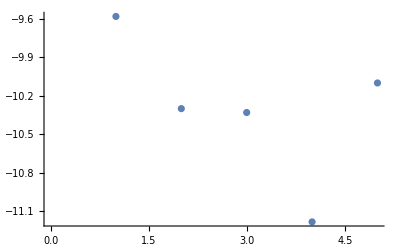

eigen functions α=1. L=0

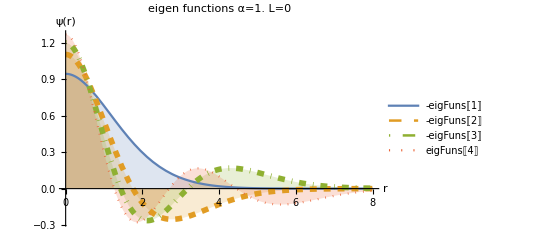

```mathematica
ListPlot[err]
labelText = "eigen functions α="<>ToString[1.0 alpha]<>" L="<>ToString[L]
figure = Plot[{-eigFuns[[1]],-eigFuns[[2]],-eigFuns[[3]],eigFuns[[4]]},{r,0,8}, PlotRange->All,PlotStyle->{Thick,{Dashed, Thickness[0.01]},{DotDashed, Thickness[0.01]}, Dotted},  PlotLegends->"Expressions", PlotLabel->labelText, AxesLabel->{"r", "ψ(r)"},Filling->Axis]
```